# Code

```mathematica
file = "../results/res11p2-target-180";
```

```mathematica
importResults[file]
```

```mathematica
restest = {"An-t1-l0"->{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},"Ao-t1-l0"->{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},"Ap-t1-l0"->{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},"Bn-t1-l1"->{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},"Bo-t1-l1"->{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},"Bp-t1-l1"->{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}
```

{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}

```mathematica
parseDirName["Bp-t1-l0"]
```

{Bp,1,0}

```mathematica
reorderRules[restest]
```

{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657}}

```mathematica
reorderResults[restest]
```

{{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325}},{Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657}}}

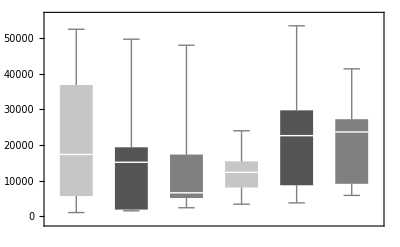
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
boxChartOfResults[file]
```

```mathematica
res2 = importResults["../results/res2"];
```

```mathematica
"An-t1-l0" /. res2
```

{18521,8407,5676,428,30750,27739,12113,24747,6493,41204,15982,22249,4995,5717,52840,28573,29058,23238,3308,11564,53140,21519,19837,2602,5513,32958,279,736,6140,2337,11416,33612,1378,9337}

```mathematica
% // Length
```

34

```mathematica
standardErrorOfMean[%369]
```

(√(60336233137/33))/17

```mathematica
% //N
```

2515.26

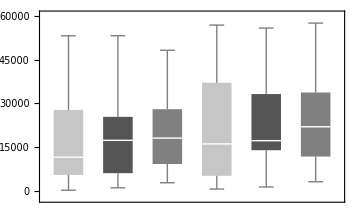
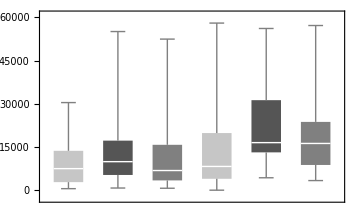
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bp-t1-l0
-Graphics- | Bo-t1-l0
-Graphics--Graphics- | An-t1-l1
-Graphics- | Ap-t1-l1
-Graphics- | Ao-t1-l1
-Graphics- | Bn-t1-l1
-Graphics- | Bp-t1-l1
-Graphics- | Bo-t1-l1

```mathematica
Column[Map[boxChartOfResults, reorderResults[res2]]]
```

```mathematica
chartLabelsHelper[keys[restest]]
```

{,,A,,,B}

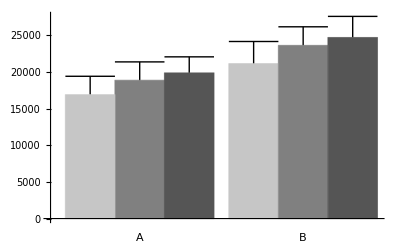
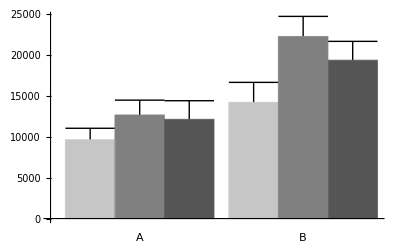
-Graphics--Graphics- | n
-Graphics- | p
-Graphics- | o
-Graphics--Graphics- | n
-Graphics- | p
-Graphics- | o

```mathematica
Column[Map[chartOfResults, reorderResults[res2]]]
```

```mathematica
sampleStandardDeviation[Range[5]]
```

5/(2 √2)

```mathematica
StandardDeviation[{4,2,5,8,6}] // N
```

2.23607

```mathematica
sampleStandardDeviation[{4,2,5,8,6}] // N
```

2.23607

```mathematica
Mean[Range[5]]
```

3

```mathematica
(Range[5] - 3)^2
```

{4,1,0,1,4}

```mathematica
Total[%]
```

10

```mathematica
(10/5)^(1/2)
```

√2

```mathematica
(n -1)^(-1/2)
```

1/(√(-1+n))

```mathematica
% // N
```

1.76777

# Read Results

```mathematica
<<loadall`
```

```mathematica
loadall[];
```

T::shdw: Symbol "T" appears in multiple contexts {"DifferentialEquations`NDSolveProblems`", "Global`"}; definitions in context "DifferentialEquations`NDSolveProblems`" may shadow or be shadowed by other definitions.

```mathematica
link = Install["run-simulation-mlink"];
```

```mathematica
Uninstall[link]
```

/Users/shane/School/sussex/thesis/code/src/run-simulation-mlink

```mathematica
Clear[runSimulationMlink]
```

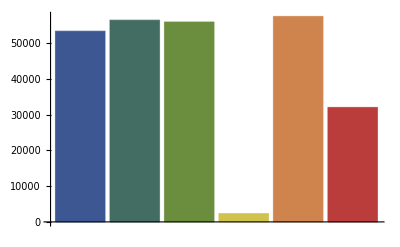
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["res9p-target"]
```

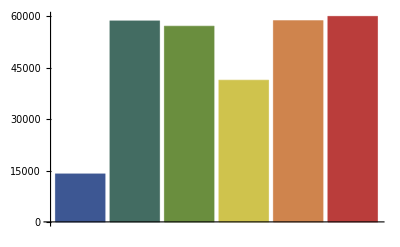
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["res8p-target"]
```

```mathematica
chartOfResults["../results/res11p2-target-180"]
```

-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["../results/res1"]
```

-Graphics--Graphics- | An-t1-l0
-Graphics- | An-t1-l1
-Graphics- | Ao-t1-l0
-Graphics- | Ao-t1-l1
-Graphics- | Ap-t1-l0
-Graphics- | Ap-t1-l1
-Graphics- | Bn-t1-l0
-Graphics- | Bn-t1-l1
-Graphics- | Bo-t1-l0
-Graphics- | Bo-t1-l1
-Graphics- | Bp-t1-l0
-Graphics- | Bp-t1-l1

```mathematica
restest
```

{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}

```mathematica
restest
```

{An-t1-l0→{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},Ao-t1-l0→{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},Ap-t1-l0→{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},Bn-t1-l1→{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},Bo-t1-l1→{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},Bp-t1-l1→{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}

```mathematica
values[restest]
```

{{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}

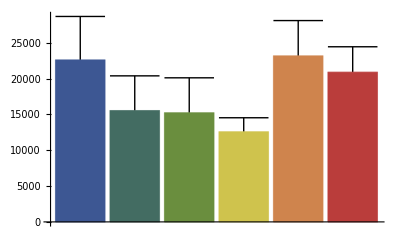
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l1
-Graphics- | Bo-t1-l1
-Graphics- | Bp-t1-l1

```mathematica
chartOfResults[restest]
```

```mathematica
MannWhitneyTest[{%117[[1]], %117[[3]]}]
```

0.384673

```mathematica
values[%]
```

{{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}

```mathematica
importResults["res8p-target"]
```

{An-t1-l0→{14000,14000,14000,14000,14000},Ao-t1-l0→{58680,58680,58680,58680,58680},Ap-t1-l0→{57131,57131,57131,57131,57131},Bn-t1-l0→{41363,41363,41363,41363,41363},Bo-t1-l0→{58757,58757,58757,58757,58757},Bp-t1-l0→{59998,59998,59998,59998,59998}}

```mathematica
importResults["res9p-target"]
```

{An-t1-l0→{53339},Ao-t1-l0→{56420},Ap-t1-l0→{55910},Bn-t1-l0→{2326},Bo-t1-l0→{57461},Bp-t1-l0→{32012}}

```mathematica
oq6 /. params
```

(3 π)/4

```mathematica
Options[drawFrogCheap]={showDistance->False,plotRange->Automatic,toTarget->None,showStart->False,showTarget->None};
```

```mathematica
drawFrogCheap[{q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_},r_,l_,fl_,OptionsPattern[]]:=
Module[{M3, R, T, O, T1, T4j, T5j, T6j, T7j, T8j, pt, p4j, T4l, T5l, T6l, T7l, T8l, p5j, p6j, p7j, p8j, oq5, oq6, oq7, oq8,
(* options *)
	target, range, distanceLine,targetLine,startDisk,targetDisk},
(* Options code *)
	target={0,0};
	distanceLine=If[OptionValue[showDistance]===True,{Black,Line[{{0,0},{q1,q2}}]},
	{}];
targetLine=If[OptionValue[toTarget]===None,
	{},target=OptionValue[toTarget];
{Black,Line[{{q1,q2},target}]}];

startDisk=If[OptionValue[showStart]===False,{},{Point[{0,0}]}];

targetDisk=If[OptionValue[showTarget]===None,{},target=OptionValue[showTarget];
{Point[target]}];

range=If[OptionValue[plotRange]===Automatic,chooseRange[7(r){{-.5,.5},{-.5,.5}},{{q1,q2},{0,0},target},2#&],OptionValue[plotRange]];



	T = TranslationTransform;
	R  = RotationTransform;
	oq5 = Pi/4;
	oq6 = 3 Pi/4;
	oq7 = 5 Pi/4;
	oq8 = 7 Pi/4;
	T1 = T[{q1,q2}];
	O = T1[{0,0}];
	M3 = R[q3];
	(*T4j =R[q3] .  T[{0, -r}];*)
	T4j = R[q3] [{0, -r}]  ;
	T5j = (R[oq5] . R[q3])[{0, -r}];
	T6j = (R[oq6] . R[q3] )[{0, -r}];
	T7j = (R[oq7] . R[q3] )[{0, -r}];
	T8j = (R[oq8] . R[q3] )[{0, -r}];
	T4l =  T[(M3 . R[q4])[{0, -l}]];
	T5l =  T[(M3 . R[q5] . R[oq5])[{0, -fl}]];
	T6l =  T[(M3 . R[q6] . R[oq6])[{0, -fl}]];
	T7l =  T[(M3 . R[q7] . R[oq7])[{0, -fl}]];
	T8l =  T[(M3 . R[q8] . R[oq8])[{0, -fl}]];
	
	Graphics[{{Circle[O, r],
		Line[{p4j = T1[T4j],T4l[p4j]}],
		Line[{p5j = T1[T5j],T5l[p5j]}],
		Line[{p6j = T1[T6j],T6l[p6j]}],
		Line[{p7j = T1[T7j],T7l[p7j]}],
		Line[{p8j = T1[T8j],T8l[p8j]}]
	},
	distanceLine,targetLine,startDisk,targetDisk
	},PlotRange->range,ImageSize->imageSize]]
```

```mathematica
imageSize = 100
```

100

```mathematica
drawFrogCheap[{1,1,.4,0,0,0,0,0}, .5, 2, 1, plotRange -> 3{{-1,1}, {-1,1}}]
```

-Graphics-

```mathematica
eval["../results/cspeed-01//An-t2-l0/r2/output.txt"]
```

0.716004

```mathematica
lookupFile["cspeed-01/An-t2-l0/r2/output.txt"]
```

../results/cspeed-01/An-t2-l0/r2/output.txt

```mathematica
lookupFile["../results/cspeed-01/An-t2-l0/r2/output.txt"]
```

./../results/cspeed-01/An-t2-l0/r2/output.txt

```mathematica
data =evalData["cspeed-01/An-t2-l0/r2/output.txt"];
```

```mathematica
data = evalData["cspeed-05/Ap-t2-l0/r2/output.txt"];
```

```mathematica
data = evalData["cspeed-01//An-t2-l0/r1/output.txt", {task -> 3}];
```

```mathematica
eval["cspeed-01//An-t2-l0/r1/output.txt", {task -> 3}]
```

0.83772

```mathematica
eval["cspeed-01//Ap-t3-l0/r2/output.txt", {task -> 3}]
```

0.401865

```mathematica
Clear[evalData]
```

```mathematica
data = evalData["cspeed-01//Ap-t3-l0/r2/output.txt", {currentSpeed -> 0.01, enableController -> True, task -> 3}];
```

```mathematica
eval["cspeed-01//Ap-t3-l0/r2/output.txt", {currentSpeed -> 0.01, enableController -> True, task -> 3, tmax -> 13}]
```

0.479102

```mathematica
Protect[showStart]
```

{showStart}

```mathematica
Options[Compile]
```

{CompilationOptions→Automatic,CompilationTarget:>$CompilationTarget,Parallelization→Automatic,RuntimeAttributes→{},RuntimeOptions→Automatic}

```mathematica
<<Developer`
```

```mathematica
Developer`SetSystemOptions["CompileReportExternal" -> True]
```

System`SetSystemOptions::obs: "Developer`SetSystemOptions" has been superseded by System`SetSystemOptions, and is now obsolete. It will not be included in future versions of Mathematica.

System`SetSystemOptions::sysname: "CompileReportExternal" is not a known SystemOption.

SetSystemOptions[CompileReportExternal→True]

```mathematica
?System`SetSystemOptions
```

System`SetSystemOptions

Attributes[System`SetSystemOptions]={Protected}

```mathematica
?System
```

Information::notfound: Symbol "System" not found.

```mathematica
System`SetSystemOptions["CompileOptions" -> "CompileReportFailure" -> True]
```

CompileOptions→{ApplyCompileLength→∞,ArrayCompileLength→250,AutoCompileAllowCoercion→False,AutoCompileProtectValues→False,AutomaticCompile→False,BinaryTensorArithmetic→False,CompileAllowCoercion→True,CompileConfirmInitializedVariables→True,CompiledFunctionArgumentCoercionTolerance→2.10721,CompiledFunctionMaxFailures→3,CompileDynamicScoping→False,CompileEvaluateConstants→True,CompileOptimizeRegisters→False,CompileReportCoercion→False,CompileReportExternal→True,CompileReportFailure→True,CompileValuesLast→True,FoldCompileLength→100,InternalCompileMessages→False,ListableFunctionCompileLength→250,MapCompileLength→100,NestCompileLength→100,NumericalAllowExternal→False,ProductCompileLength→250,ReuseTensorRegisters→True,SumCompileLength→250,SystemCompileOptimizations→All,TableCompileLength→250}

```mathematica
Remove[Developer`*]
```

```mathematica
Names["Developer`*"]
```

{BesselSimplify,BoundingBox,BoxesToMathML,CalendarData,CellInformation,CheckProtectedMode,CheckRestrictedFileName,Combobox,ComboboxBoxes,CompensatedAdd,CompensatedPlus,ContextFreeForm,CreateRegistryKey,CustomColorSetter,CustomColorSetterBoxes,DecodeBase64,EncodeBase64,EnumerateRegistrySubkeys,FibonacciSimplify,FileInformation,FilterGraphicsOptions,FindDivisions,ForceLaunch,ForceLocalFrontEnd,FourierListConvolve,FromPackedArray,FromRawArray,GammaSimplify,GenerateBitmapCaches,Graphics3DOptions,GraphicsOptions,HolonomicSimplify,InequalityInstance,InitializationFunction,InputToInputForm,InputToStandardForm,InstallFrontEnd,LaunchCommand,LaunchFlags,LegacyGraphics,LinearExpressionToMatrix,LinearExpressionToSparseMatrix,MachineComplexQ,MachineIntegerQ,MachineRealQ,MathMLToBoxes,NotebookConvert,NotebookInformation,OutputToOutputForm,OutputToStandardForm,PackedArrayForm,PackedArrayQ,PartitionMap,PolyGammaSimplify,PolyLogSimplify,PolynomialDivision,PreserveStyleSheet,PseudoFunctionsSimplify,RawArrayQ,RawCompress,RawUncompress,ReadRegistryKeyValues,RemoveRegistryKey,RemoveRegistryKeyValues,ReplaceAllUnheld,SetSystemOptions,SparseLinearSolve,StartProtectedMode,StreamToString,StringFromStream,SymbolicGraphics,SystemOptions,ThreadID,ToPackedArray,TrigToRadicals,UninstallFrontEnd,UseFrontEnd,WriteRegistryKeyValues,ZeroQ,ZetaSimplify,$MaxMachineInteger,$ProtectedMode,$SymbolShadowingFunction,$SymbolSystemShadowing,$SystemErrorCode}

```mathematica
Compile[{{x}}, Integrate[2^y, {y, 0, x}]]
```

Compile::compfail: Compilation of ∫_0 x 2^y ⅆ y failed because y was not a form suitable for the compiler.

Compile::extscalar: ∫_0 x 2^y ⅆ y cannot be compiled and will be evaluated externally. The result is assumed to be of type Integer.

CompiledFunction[{x},∫_0^x 2^y ⅆy,-CompiledCode-]

```mathematica
animateData[data, showStart -> True, showTarget -> {0, .25}, showTime -> True, showDistanceToTarget -> True, showMeanDistanceToTarget -> True]
```

```mathematica
animateData[data, showStart -> True, showTarget -> {0, .25}, showTime -> True,showMeanDistanceToTarget -> True, showDistanceToTarget -> True]
```

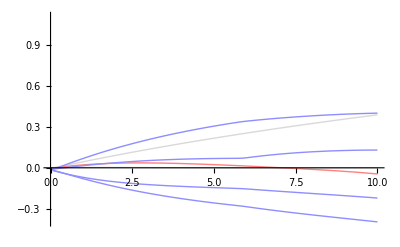

```mathematica
plotConfigurationData[data]
```